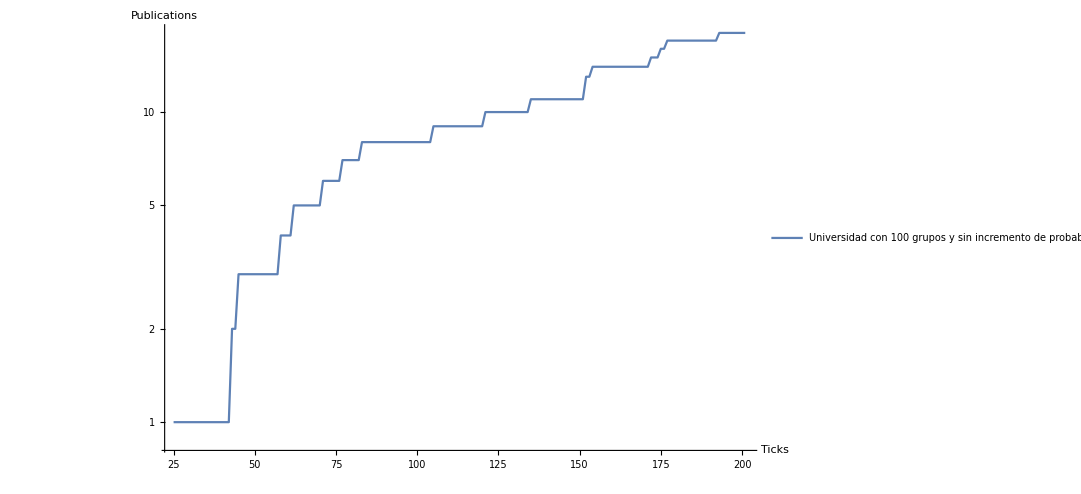

```mathematica
SetDirectory["/home/fabianact/NUEVOMODELO/PrimeraVersion"]; 
pub1= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub1-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub2= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub2-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
pub3= Import["/home/fabianact/NUEVOMODELO/PrimeraVersion/test0/testTables/pub3-100-100-100-0.001-0.001-1.0E-4-0-100-curve.csv"];
                          plotPub = Show[ListLogPlot[{ pub3},ImageSize->800,  AxesLabel->{"Ticks","Publications"},Joined->True, PlotLegends->{ "Universidad con 100 grupos
 y sin incremento de probabilidad"},PlotRange->All]]
Export["pub3-100-100-100-0.001-0.001-1.0E-4-0-100-curve.png",plotPub];
```